```mathematica
(* Breusch=Pagan test for heteroskedasticity. *)
base=DirectoryName[NotebookFileName[]];
```

```mathematica
(* Load / add data files *)
bubbleScaled =Import[base<>"../csv/bubbleScaled-1.tsv"];
```

```mathematica
bubbleDays=180 (* From the main notebook *)
```

180

```mathematica
(* Heteroscedastic? Perform Breusch-Pagan test. *)
(* 1. Fit a model. Fit hyperbolic power law function: *)
tc=.
numParams=4;
hyperbolicModel=a +(tc-ti)^m(b+c Cos[ω Log[tc-ti]]+d Sin[ω Log[tc-ti]])/.{c-> 0, d-> 0}
```

a+b (tc-ti)^m

```mathematica
(* Profiling over 0.1 < m < 0.9, 1. < tc < 3 months in the future *)
minM=0.1;
maxM=0.9;
months=3;
```

```mathematica
(* Try to estimate all the params using log-likelihood: *)
(* Define three months in the future scaled interval endpoint: *)
maxTc=(bubbleDays+30 months)/bubbleDays//N
```

1.5

```mathematica
(* Define 1 week resolution scaled interval step: *)
stepTc=7/bubbleDays//N
```

0.0388889

```mathematica
(* Define 10 days resolution scaled initial time step *)
stepTi=10/bubbleDays//N
```

0.0555556

```mathematica
(* Fixed t1: *)
t1=1/3;
bubbleSelected=Select[bubbleScaled,#[[1]]>= t1&];
```

```mathematica
fit=Block[{},m=.;tc=.;
bestFit=MaximalBy[Flatten[Table[{tc,m,nlm=NonlinearModelFit[bubbleSelected,hyperbolicModel,{a,b}, ti];nlm["BestFitParameters"],
ℛ=nlm["FitResiduals"];
(* Fit an AR(1) process *)
ar1Process=ARProcess[μ,{ρ},σ^2];
estimatedAR1Model=FindProcessParameters[ℛ,ar1Process],
Total[ℛ^2]/(Length[ℛ]-numParams),
LogLikelihood[ar1Process/. estimatedAR1Model,ℛ]},{m,minM,maxM,1./10},{tc, bubbleScaled[[-1]][[1]]+0.0001, maxTc,stepTc}],1], Last]//Flatten[#, 1]&;modelParams=Join[bestFit[[3]], {Subscript[T, 1]-> t1,tc-> bestFit[[1]],m-> bestFit[[2]],LL-> bestFit[[6]], ℛerror-> bestFit[[5]]},bestFit[[4]]]]
```

{a→1.15764,b→-0.585223,T_1→1/3,tc→1.4751,m→0.9,LL→8310.47,ℛerror→0.00472501,ρ→0.992683,σ→-0.00829335,μ→-2.27719×10^-18}

```mathematica
tc=.
tf=tc/.fit[[4]]
```

1.4751

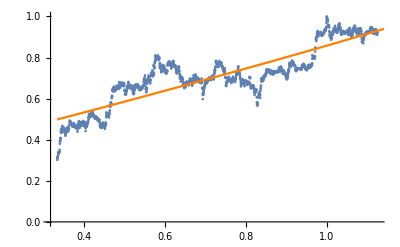

```mathematica
Show[ListPlot[bubbleSelected], Plot[Evaluate[hyperbolicModel/.fit], {ti, t1, tf}, PlotStyle->{Orange}, Evaluated->True]]
```

```mathematica
(* Fit the squared errors to a model with the same predictors :*)
(* 1. Fixing the fitted non-linear params *)
fitModel=hyperbolicModel/.fit[[4;;5]]
```

a+b (1.4751-ti)^0.9

```mathematica
ℛ2=nlm["FitResiduals"]^2;
newℛ2=Block[{newData=bubbleSelected},newData[[All,-1]]=ℛ2;newData];
```

```mathematica
nlm2=NonlinearModelFit[newℛ2,fitModel,{a,b}, ti]
```

FittedModel[0.00102015+0.00483443 (1.4751-ti)^0.9]

```mathematica
nlm2["BestFitParameters"]
```

{a→0.00102015,b→0.00483443}

```mathematica
(* 2. Not fixing the non-linear params *)
fit3=Block[{},m=.;tc=.;
bestFit=MaximalBy[Flatten[Table[{tc,m,nlm3=NonlinearModelFit[newℛ2,hyperbolicModel,{a,b}, ti];nlm3["BestFitParameters"],
ℛ=nlm3["FitResiduals"];
(* Fit an AR(1) process *)
ar1Process=ARProcess[μ,{ρ},σ^2];
estimatedAR1Model=FindProcessParameters[ℛ,ar1Process],
Total[ℛ^2]/(Length[ℛ]-numParams),
LogLikelihood[ar1Process/. estimatedAR1Model,ℛ]},{m,minM,maxM,1./10},{tc, bubbleScaled[[-1]][[1]]+0.0001, maxTc,stepTc}],1], Last]//Flatten[#, 1]&;modelParams=Join[bestFit[[3]], {Subscript[T, 1]-> t1,tc-> bestFit[[1]],m-> bestFit[[2]],LL-> bestFit[[6]], ℛerror-> bestFit[[5]]},bestFit[[4]]]]
```

{a→0.00255585,b→0.00468929,T_1→1/3,tc→1.1251,m→0.8,LL→12678.6,ℛerror→0.0000328181,ρ→0.972755,σ→-0.001327,μ→1.08732×10^-20}

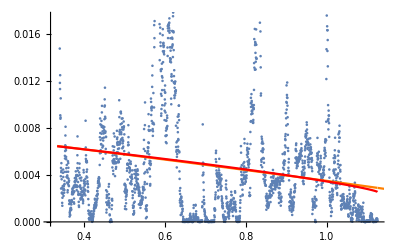

```mathematica
(* Plot *)
Show[ListPlot[newℛ2], Plot[{Evaluate[fitModel/.nlm2["BestFitParameters"]],Evaluate[hyperbolicModel/.fit3]}, {ti, t1, tf}, PlotStyle->{Orange, Red}, Evaluated->True]]
```

```mathematica
breuschPagan2=(Variance[ℛ2](Length[bubbleSelected]-1)-Total[nlm2["FitResiduals"]^2])/(2(Total[ℛ2]/Length[bubbleSelected])^2)
```

56.5369

```mathematica
breuschPagan3=(Variance[ℛ2](Length[bubbleSelected]-1)-Total[nlm3["FitResiduals"]^2])/(2(Total[ℛ2]/Length[bubbleSelected])^2)
```

56.5369

```mathematica
(* Compute the p-value: *)
1-CDF[ChiSquareDistribution[Length[nlm["BestFitParameters"]]-1],breuschPagan3]
```

5.51781×10^-14